# Numeric sketch of proof

In this experiment I generate 50000 pseudorandom numbers with a power-law distribution defined as

```mathematica
PDF[ZipfDistribution[0.95],l]
```

Piecewise[{{0.590169/l^1.95, l≥1}, {0, True}}]

A sorted number sequence with this distribution, defined as l, is analogous to the wrongly calculated record breaking waiting time that it was actually a plain  record breaking time.

An exampe of 50 sorted pseudorandom numbers generated with a power-law distribution.

```mathematica
Sort[RandomVariate[ZipfDistribution[0.95],50]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,3,3,4,5,5,6,9,14,20,25,26}

It is possible to obtain the record breaking waiting time sequence k from the record breaking time sequence l by taking the differences between record breaking times.

```mathematica
Diff[seq_, lag_:1]:= Drop[seq, lag] - Drop[seq, -lag];
```

```mathematica
Diff[Sort[RandomVariate[ZipfDistribution[0.95],50]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,3,2,18,15}

For the k distribution, 10000 sequences of 200 transformed points were generated. The results are shown below.

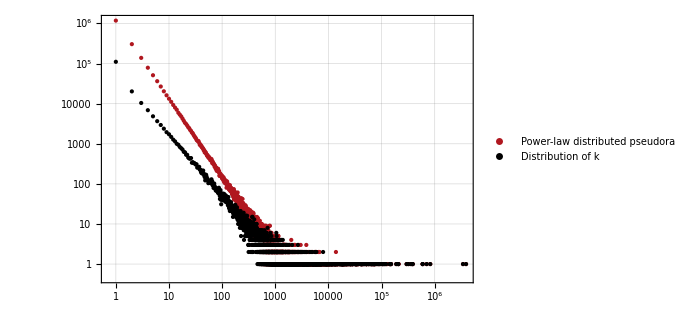

```mathematica
rawData = Table[RandomVariate[ZipfDistribution[0.95],200],10000];
data1 = Flatten[rawData];
data2 = Flatten[Map[Diff[Sort[#]]&,rawData]];

HistogramPointPlot[
{data1,data2},
ScalingFunctions->{"Log","Log"},
PlotLegends->Placed[
LineLegend[
{"Power-law distributed pseudorandom numbers l", "Distribution of k"},
LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),
LabelStyle->11
],
{Right,Top}
]
]
```

```mathematica
Map[FindDistribution,{data1,data2}]
```

$Aborted

Conclusion: If record times are distributed as a power-law, then record waiting times must also be distributed as a power-law.

- To check the other way around: Make partial sum.

## Test 1

Numeric

```mathematica
DynamicModule[{𝒟1,𝒟2,data1,data2,pltData1,pltData2},
Manipulate[
𝒟1=ZipfDistribution[0.95];
𝒟2=TransformedDistribution[u+c,u\[Distributed]𝒟1];
data1 = RandomVariate[𝒟1,10000];
data2 = RandomVariate[𝒟2,10000];

pltData1 = HistogramPoints[data1];
pltData2 = HistogramPoints[data2];

ListPlot[
{pltData1,pltData2},
ScalingFunctions->{"Log","Log"},
Joined->{True,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->Take[Map[{#,{PointSize[Large],#}}&,colors],2],
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]]
]
,
{{c,1},-5,5,0.2},
SaveDefinitions->True,
TrackedSymbols:>{c}
]
]
```

Analytic

```mathematica
f1[k_,c_]:=PDF[TransformedDistribution[u+c,u\[Distributed]ZipfDistribution[40,0.05]],k];
f2[k_]:=PDF[ZipfDistribution[40,0.05],k];

DynamicModule[{data1,data2,data3},
Manipulate[
data1 = Table[{k,f1[k,c]},{k,1,1000,1}];
data2 = Table[{k,f2[k]},{k,1,1000,1}];
data3 = Table[{k,f2[k]-c},{k,1,1000,1}];

ListPlot[
{data1,data2,data3},
Joined->True,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{Red,Blue,Green},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["PDF",15]}, 
ScalingFunctions->{"Log","Log"}
],
{{c,0},-5,5,0.5}
]
]
```

Conclusion: The power-law distribution plus a constant causes the log-log plot to deform.

## Test 2

```mathematica
data = RecordTimesStatistic[market,40];
pltData = HistogramPoints[data,Automatic,"PDF"];
fitData = Table[PDF[ZipfDistribution[40,0.0599349401480466],k],{k,1,Max[data],1}];

data2 = RecordTimesDiffStatistic[market,40];
pltData2 = HistogramPoints[data2,Automatic,"PDF"];
```

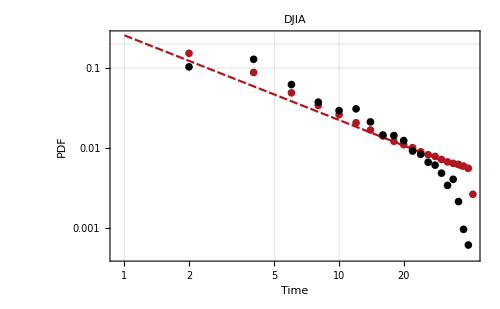

```mathematica
ListPlot[
{pltData,fitData,pltData2},
Joined->{False,True,False},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]},Black},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["PDF",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->{"Log","Log"}
]
```

```mathematica
CoolerZipf[k_,c_,n_,ρ_]:=(-c+k)^(-1-ρ)/HarmonicNumber[n,1+ρ];
DynamicModule[{fitData},
Manipulate[
fitData = Table[CoolerZipf[k,c,40+a,0.0599349401480466],{k,1,Max[data],1}];

ListPlot[
{fitData,pltData2},
Joined->{True,False},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{{PointSize[Large],First[colors]},Black},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["PDF",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->{"Log","Log"}
],
{{a,0},-40,40,1},
{{c,0},-10,10,1}
]
]
```

```mathematica
DynamicModule[{fitData},
Manipulate[
fitData = Table[PDF[TransformedDistribution[u+c,u\[Distributed]ZipfDistribution[40+a,0.0599349401480466]],k],{k,1,Max[data],1}];

ListPlot[
{fitData,pltData2},
Joined->{True,False},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{{PointSize[Large],First[colors]},Black},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
PlotRange->All,
FrameLabel->{Style["Time",15], Style["PDF",15]}, 
PlotLabel->market["Name"],
ScalingFunctions->{"Log","Log"}
],
{{a,0},-40,40,1},
{{c,0},-10,10,1}
]
]
```